```mathematica
GinibreMatrix[m_,n_]:=RandomReal[NormalDistribution[0,1],{m,n}];
```

```mathematica
GinibreMatrix[2,2]
```

{{-0.668443,1.33187},{-0.210609,-0.680666}}

```mathematica
x=RandomReal[{0,1},{4,4}];
```

{{0.0136569,0.0754717},{0.83775,0.304428}}

{0.351355,0.589577-0.727289 ⅈ}

```mathematica
rKets[l_]:=Block[{kets,prod},
kets=Table[RandomKet[l[[i]]],{i,1,Length[l]}];
prod=kets[[1]];
(*For[i=1,i<Length[kets],
prod=Flatten[{prod}⊗kets[[i+1]]]
];*)
kets
]
```

```mathematica
a=Flatten[Fold[KroneckerProduct,{1}, rKets[{3,2}]]]
```

{0.660708+0. ⅈ,0.443388-0.00207358 ⅈ,0.0686462-0.0938945 ⅈ,0.0457724-0.0632261 ⅈ,0.212744-0.440637 ⅈ,0.141385-0.29637 ⅈ}

```mathematica
x=RandomReal[{0,1},{4,4}];
```

```mathematica
RandomProductNumericalRange::usage = "RandomLocalNumericalRange[M,{dim1,dim2,...,dimN},n] returns n points from the product numerical range of the matrix M with respect to division specified as {dim1,dim2,...,dimN}. Note that dim1×dim2×...×dimN must be equal to the dimension of matrix M.";
```

```mathematica
RandomProductNumericalRange[x,{2,2},4]
```

{0.643582-0.150487 ⅈ,0.561209-0.0362911 ⅈ,0.595493-0.00141139 ⅈ,0.517677+0.0609187 ⅈ}

```mathematica
RandomProductNumericalRange[A_,sys_,noPoints_:1]:=Block[{prod},
Table[prod=RandomProductState[sys];Tr[Proj[prod].A],{noPoints}]
];
```

```mathematica
RandomProductKet[l_]:=Flatten[Apply[KroneckerProduct,Table[RandomKet[l[[i]]],{i,1,Length[l]}]]];
```

```mathematica
RandomProductKet[{2,2}]
```

{0.802422+0. ⅈ,0.0246818+0.474068 ⅈ,0.309706-0.0307995 ⅈ,0.0277225+0.182026 ⅈ}

```mathematica
KroneckerProduct[RandomProductState[{2,2}]]
```

KroneckerProduct::argmu: KroneckerProduct called with 1 argument; 2 or more arguments are expected.

KroneckerProduct[{{0.400167,-0.828564-0.391596 ⅈ},{0.284187,-0.264418+0.921586 ⅈ}}]

```mathematica
KroneckerProduct/@RandomProductState[{2,2}]
```

KroneckerProduct::argmu: KroneckerProduct called with 1 argument; 2 or more arguments are expected.

{KroneckerProduct[{0.677838,-0.7172+0.161739 ⅈ}],KroneckerProduct[{0.652869,0.639811+0.405467 ⅈ}]}

```mathematica
stany=RandomProductState[{2,2,2}]
```

{{0.864548,-0.0736578+0.497123 ⅈ},{0.290112,-0.674164+0.679219 ⅈ},{0.732451,0.139138-0.666451 ⅈ}}

```mathematica
Flatten[{Flatten[{stany[[1]]}⊗stany[[2]]]}⊗stany[[3]]]
```

{0.18371+0. ⅈ,0.0348979-0.167156 ⅈ,-0.426907+0.430107 ⅈ,0.310255+0.470143 ⅈ,-0.0156517+0.105635 ⅈ,0.0931431+0.034308 ⅈ,-0.210944-0.28212 ⅈ,-0.29677+0.138344 ⅈ}

```mathematica
Flatten[Apply[KroneckerProduct,stany]]
```

{0.18371+0. ⅈ,0.0348979-0.167156 ⅈ,-0.426907+0.430107 ⅈ,0.310255+0.470143 ⅈ,-0.0156517+0.105635 ⅈ,0.0931431+0.034308 ⅈ,-0.210944-0.28212 ⅈ,-0.29677+0.138344 ⅈ}

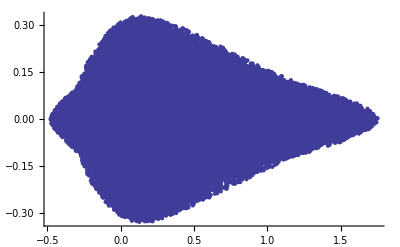

```mathematica
ListPlot[ComplexToPoint[RandomProductNumericalRange[x,{2,2},100000]]]
```

```mathematica
??ComplexToPoint
```

ComplexToPoint[z] returns real and imaginary parts of a complex number z as a pair of real numbers (point in SuperscriptBox["R", "2"]).

Attributes[ComplexToPoint]={Listable}
 
ComplexToPoint[z_]:={Re[z],Im[z]}